```mathematica
ClearAll["Global`*"]
```

```mathematica
c={0.5,0.5};
r=0.2;
d=0;
L=1.2553455316455193;
```

```mathematica
norm[θ_]:=θ-2π Floor[θ/(2π)]
```

```mathematica
ys[x_]:=c+r{Cos[2π x/L],Sin[2π x /L]}
U[x_]:={d Cos[2π 3 x/L] Cos[2π x/L],d Cos[2π 3x /L]Sin[2π x /L]}
X[x_]:=ys[x]+U[x]
ψ[x_]:=-ArcTan[X'[x][[1]],X'[x][[2]]]
ψ0[x_]:=-2 π x/L
dψ[x_]:=norm[ψ[x]-ψ0[x]]
ν[x_]:=Norm[X'[x]]
l[x_]:=NIntegrate[Sqrt[g[y]],{y,0,x}]

e[x_]:=X'[x]
g[x_]:=e[x].e[x]
gc[x_]:=1/g[x]
n[x_]:={-e[x][[2]],e[x][[1]]}/Sqrt[g[x]]
b[x_]:=n[x].e'[x]
H[x_]:=1/2 gc[x]b[x]
```

```mathematica
(*check X*)
```

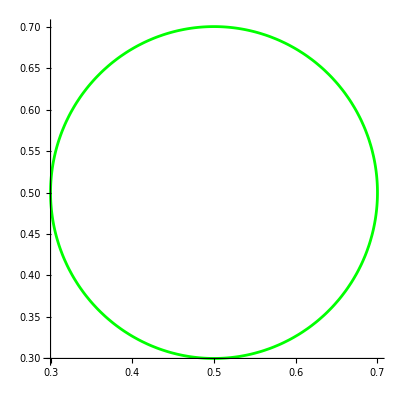

```mathematica
plotexX =ParametricPlot[X[x],{x,0,L},PlotStyle->Green]
```

```mathematica
(*Plot the x and y components of U_n_12*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_10.csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

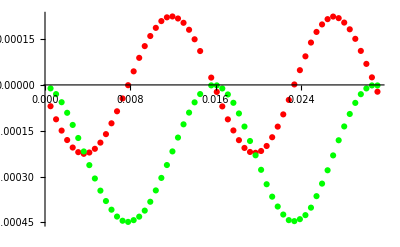

```mathematica
Show[ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Red],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green],PlotRange->Full]
```

```mathematica
(*check nu*)
```

```mathematica
plotexν=ParametricPlot[{l[x],Norm[e[x]]},{x,0,L},PlotStyle->Green]
```

-Graphics-

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/nu_n_12_20.csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

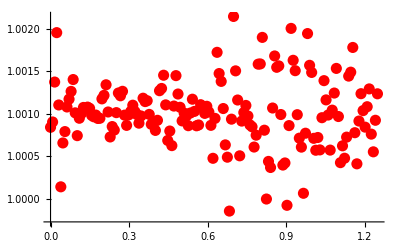

```mathematica
plotnumν=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

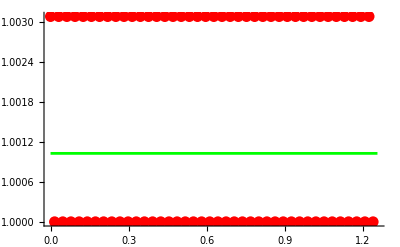

```mathematica
Show[plotnumν,plotexν,PlotRange->Full]
```

```mathematica
(*check psi*)
```

```mathematica
plotexψ=ParametricPlot[{l[x],norm[-ArcTan[e[x][[1]],e[x][[2]]]-ψ0[x]]},{x,0,L},PlotStyle->Green]
```

-Graphics-

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/dpsi_n_12_10.csv"][[2;;]];
t=Table[{t[[i,2]],norm[t[[i,1]]]},{i,2,Length[t]}]
```

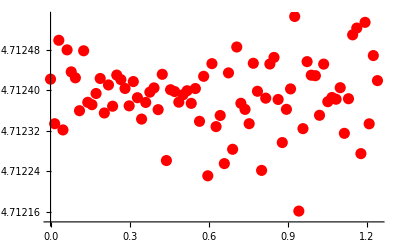

```mathematica
plotnumψ=ListPlot[t,PlotStyle->{Red,PointSize->0.02},Plot]
```

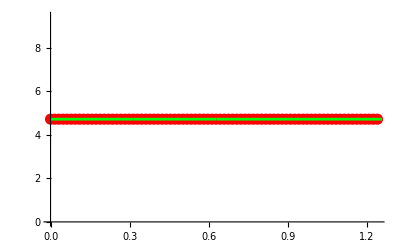

```mathematica
Show[plotnumψ,plotexψ]
```

```mathematica
(*check mu*)
```

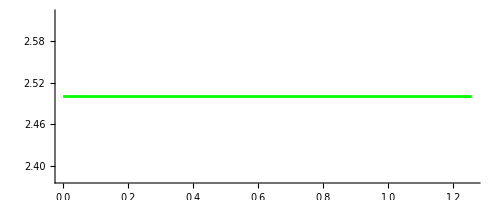

```mathematica
plotexμ=ParametricPlot[{l[x],H[x]},{x,0,L},PlotStyle->Green]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/mu_n_12_20.csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.0145538,100.075},{0.0166329,100.068},{0.0124747,100.057},{0.0135143,100.066},{0.0187121,100.04},{0.0176725,100.054},{0.0103956,100.026},{0.0114351,100.04},{0.0207912,100.011},{0.0197516,100.024},{0.00831647,100.002},{0.00935603,100.012},{0.0228703,99.9985},{0.0218307,100.002},{0.00623735,100.002},{0.00727691,99.9992},{0.0249494,100.012},{0.0239098,100.003},{0.00415823,100.025},{0.00519779,100.011},{0.0270285,100.041},{0.025989,100.025},{0.00207912,100.056},{0.00311868,100.039},{0.0291076,100.068},{0.0280681,100.055},{0.0311868,100.074},{0.00103956,100.066},{0.0301472,100.072}}

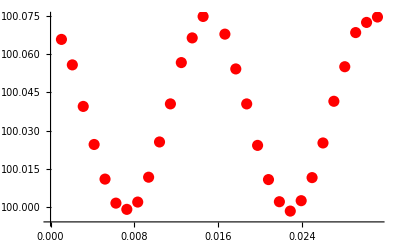

```mathematica
plotnumμ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

Show::gcomb: Could not combine the graphics objects in Show[,plotexμ].

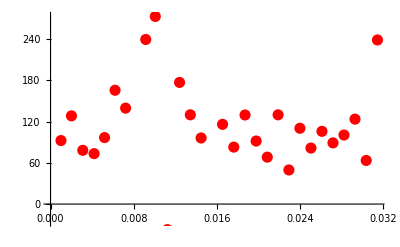
Show[-Graphics-,plotexμ]

```mathematica
Show[plotnumμ,plotexμ]
```